# Hints for a gravitational constant transition in Tully-Fisher data - G. Alestas, I. Antoniou and L. Perivolaropoulos - Figure 2

## General Settings

### Setting the Environment

```mathematica
SetDirectory[NotebookDirectory[]]
Off[General::obspkg,First::nofirst,InterpolatingFunction::dmval,FindMinimum::lstol,FindMinimum::lstol];
```

### Importing Data

```mathematica
data5=Import["Data//Lel19a.dat","Data"]
ndat5=Length[data5];
```

```mathematica
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
```

```mathematica
test1=Table[{data5[[i,6]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]},{i,1,ndat5}];
```

```mathematica
tests9=Select[test1,#[[1]]<9 &];
testl9=Select[test1,#[[1]]>9 &];
tests17=Select[test1,#[[1]]<17 &];
testl17=Select[test1,#[[1]]>17 &];
```

```mathematica
emcee9s=Table[{tests9[[i,3]],tests9[[i,5]],tests9[[i,4]],tests9[[i,6]]},{i,1,Length[tests9]}];
emcee9l=Table[{testl9[[i,3]],testl9[[i,5]],testl9[[i,4]],testl9[[i,6]]},{i,1,Length[testl9]}];
emcee17s=Table[{tests17[[i,3]],tests17[[i,5]],tests17[[i,4]],tests17[[i,6]]},{i,1,Length[tests17]}];
emcee17l=Table[{testl17[[i,3]],testl17[[i,5]],testl17[[i,4]],testl17[[i,6]]},{i,1,Length[testl17]}];
```

```mathematica
Export["Lel19_9s.dat",emcee9s]
Export["Lel19_9l.dat",emcee9l]
Export["Lel19_17s.dat",emcee17s]
Export["Lel19_17l.dat",emcee17l]
```

Lel19_9s.dat

Lel19_9l.dat

Lel19_17s.dat

Lel19_17l.dat

```mathematica
test1r=Table[{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]},{i,1,ndat5}]
```

{{8.0287,0.39,1.76118,0.0308388,8.68,0.05},{4.27556,0.2,1.6721,0.0156979,8.59,0.06},{8.14791,2.25,1.82151,0.0301116,9.32,0.26},{4.10864,0.21,1.72997,0.0299032,8.81,0.06},{15.5472,4.62,1.77815,0.0267633,9.1,0.26},{28.8606,7.17,2.24304,0.011904,10.48,0.24},{14.4944,3.9,2.03782,0.015912,9.55,0.27},{60.0683,9.1,2.49776,0.0169682,11.27,0.16},{78.4852,8.06,2.05038,0.111688,9.72,0.1},{51.8429,10.7,2.1452,0.0180186,9.87,0.19},{97.0329,9.68,1.99034,0.0412699,9.9,0.1},{29.1097,8.85,1.93349,0.0399604,9.52,0.22},{3.78269,0.2,1.82217,0.0392169,9.28,0.06},{102.748,10.,2.38489,0.0200363,11.03,0.13},{7.42265,2.04,1.52763,0.0347715,8.29,0.26},{7.30575,0.36,2.02653,0.0347037,9.45,0.09},{2.01214,0.11,1.93247,0.0273785,9.64,0.08},{18.5847,0.2,1.94498,0.0428581,9.63,0.27},{3.75456,0.19,2.02078,0.0376492,9.78,0.08},{20.325,5.2,2.21219,0.0473939,10.86,0.22},{1.94111,0.1,1.96988,0.0934984,9.43,0.08},{79.8658,8.07,2.34262,0.0138028,11.27,0.13},{9.70262,0.5,2.33465,0.0124516,10.88,0.11},{11.3352,3.42,2.0406,0.0229253,10.05,0.26},{50.8659,9.25,2.2159,0.0150474,10.68,0.23},{3.29697,0.16,2.11793,0.0201784,9.97,0.08},{8.99765,0.49,2.18752,0.0321273,10.62,0.11},{13.459,1.4,2.45454,0.0233153,11.03,0.13},{8.2985,1.98,2.26623,0.0176327,10.65,0.28},{4.09192,0.2,1.92169,0.0415808,9.,0.06},{3.6915,0.18,1.93146,0.0487869,9.28,0.11},{72.1829,10.2,2.32201,0.0196427,11.03,0.15},{1.35491,0.07,1.82086,0.025568,8.86,0.06},{12.4454,1.4,2.17638,0.0135896,10.53,0.11},{12.7004,2.3,2.3298,0.0343219,10.68,0.28},{20.2931,2.5,2.22531,0.0341,10.64,0.15},{3.07097,0.17,1.69984,0.0268543,8.41,0.06},{20.2832,2.5,2.07408,0.0373255,10.22,0.14},{17.9871,2.5,2.22634,0.0159786,10.58,0.16},{20.0362,2.5,2.24055,0.0364161,10.57,0.15},{22.7066,2.5,2.13322,0.016287,10.13,0.15},{19.5693,2.5,2.21219,0.0428675,10.37,0.15},{19.5748,2.5,2.344,0.0157246,10.87,0.16},{14.1332,2.5,2.12287,0.0176609,9.94,0.15},{23.5216,2.3,2.38202,0.0167477,11.13,0.13},{16.0259,2.5,2.09968,0.0189746,10.09,0.14},{16.1295,2.5,2.23779,0.0188259,10.64,0.16},{20.0426,2.5,2.1959,0.0301312,10.71,0.16},{14.6356,2.5,2.11893,0.0214525,10.1,0.15},{19.5394,2.5,2.23477,0.0212324,10.81,0.15},{14.7938,2.5,2.19921,0.0224956,10.53,0.15},{15.3917,2.5,2.1682,0.0530346,10.38,0.16},{18.1223,2.5,2.26647,0.0218527,10.8,0.15},{15.5222,2.5,2.04376,0.0258987,10.,0.14},{18.5011,2.5,2.2584,0.0217838,10.66,0.16},{7.61443,0.2,2.0835,0.0200528,10.24,0.27},{17.0407,1.5,2.41863,0.0377391,10.96,0.13},{21.9708,4.7,2.28825,0.0105036,10.85,0.27},{10.0188,0.5,2.25285,0.0344291,10.96,0.1},{28.9235,9.92,2.32118,0.0153298,11.27,0.24},{4.96129,2.12,1.95569,0.0177829,9.57,0.27},{17.0347,0.9,2.33244,0.0076707,11.06,0.1},{50.5945,0.2,2.46776,0.0155211,11.08,0.24},{23.7142,5.1,2.1878,0.0228125,10.38,0.27},{116.065,12.8,2.40088,0.0260366,11.35,0.13},{6.06269,0.31,2.06558,0.0123147,9.94,0.09},{51.0244,10.2,2.38256,0.0343531,11.18,0.19},{1.83165,1.66,2.20112,0.0404229,10.61,0.28},{13.6788,1.5,2.3784,0.0112586,11.15,0.13},{14.0788,0.72,2.34025,0.014275,10.59,0.11},{54.1777,9.7,2.11261,0.0502315,10.2,0.14},{10.2296,3.75,1.8651,0.0236835,9.41,0.26},{5.38596,0.1,1.74194,0.0330217,8.75,0.06},{11.5574,3.1,1.93551,0.0312158,9.18,0.26},{72.0915,10.4,2.52114,0.0533349,11.43,0.16},{70.587,8.06,2.46165,0.0238363,11.41,0.12},{82.495,9.8,2.26174,0.0410958,10.97,0.15},{15.6744,4.95,2.42308,0.0273605,11.15,0.28},{66.922,10.,2.34163,0.0215419,10.84,0.2},{22.2008,7.2,2.29425,0.0337237,10.73,0.24},{34.1095,5.2,2.10106,0.0192583,10.09,0.23},{12.6764,0.2,1.96095,0.034663,9.33,0.26},{7.7947,2.88,1.95856,0.0305567,9.28,0.27},{5.26199,3.75,1.86213,0.0262308,9.35,0.26},{42.978,5.72,2.3298,0.0434609,11.03,0.23},{17.8646,5.3,1.86392,0.0558085,9.24,0.22},{7.93722,1.85,1.90146,0.0424743,9.01,0.26},{9.15988,2.59,2.05308,0.0188195,9.77,0.27},{17.8712,2.5,1.92942,0.0265506,9.31,0.14},{14.7483,3.6,1.91487,0.0369586,9.37,0.26},{89.7365,8.87,2.3006,0.11165,10.96,0.12},{20.418,2.5,1.92324,0.0201981,9.25,0.13},{28.855,7.32,2.34124,0.0193856,10.64,0.24},{22.6898,5.32,2.39463,0.0134696,10.75,0.24},{20.3194,2.5,1.85248,0.0390112,9.35,0.13},{16.4541,2.5,2.03623,0.0247544,9.79,0.14},{19.0244,2.5,1.90091,0.0278065,9.4,0.14},{17.0058,2.5,2.03019,0.0663955,9.94,0.13},{14.6988,2.5,2.03743,0.0310569,9.82,0.13},{13.1679,5.9,1.81425,0.018638,9.88,0.26},{7.06966,0.34,1.86629,0.0218476,9.29,0.08},{7.52064,2.53,2.01284,0.026967,9.2,0.27},{5.06352,0.24,1.90091,0.0310779,9.55,0.06},{5.73766,1.41,1.78958,0.02325,8.73,0.26},{11.6535,2.43,1.75891,0.0551951,8.98,0.27},{6.63489,0.33,1.91593,0.0131675,9.17,0.06},{4.97264,0.53,1.89542,0.0287125,9.17,0.11},{6.3401,2.,1.75511,0.0175431,8.72,0.26},{37.1936,9.82,2.26102,0.0268871,10.48,0.24},{62.7269,8.4,2.1827,0.0424596,10.78,0.11},{65.4773,11.4,2.35564,0.0352099,11.27,0.19},{17.6452,4.6,1.8537,0.0747647,9.39,0.27},{73.4098,11.8,2.4304,0.013049,11.31,0.16},{18.0787,5.1,2.45954,0.0650774,10.88,0.28},{109.507,10.1,2.36922,0.0324573,11.07,0.11},{14.0958,2.93,1.85552,0.0296597,9.47,0.26},{4.1411,0.22,1.75128,0.0323191,8.62,0.06},{1.08834,0.05,1.5682,0.0738973,7.98,0.06}}

```mathematica
tabdssd1={};
Do[
sint=0.077;
tabdssd={};
tabbfic={};
test1r=Table[{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]},{i,1,ndat5}];
Do[
tests=Select[test1r,#[[1]]<dsplt &];
testl=Select[test1r,#[[1]]>dsplt &];

chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]];
slmins=mintfs[[2,2,2]];
mintfsc=mintfs[[1]];

chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]];
slminl=mintfl[[2,2,2]];
mintflc=mintfl[[1]];
dchi1=chi2tfl[icmins,slmins]-mintflc;
dchi2=chi2tfs[icminl,slminl]-mintfsc;
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
AppendTo[tabbfic,{dsplt,icmins,icminl}];
AppendTo[tabdssd,{dsplt,sdistmin}],{dsplt,2,70,1}];
AppendTo[tabdssd1,tabdssd],{k,1,100}]
tabfin1={};
tabfin2={};
tabfin3={};
tabfin={};
Do[
AppendTo[tabfin1,Mean[Table[{j,tabdssd1[[n,j-1,2]]},{n,1,100}]]],{j,2,70}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
tabfin2={};
tabfin3={};
Do[
AppendTo[tabfin2,Mean[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]][[1]]+StandardDeviation[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]][[1]]],{j,2,70}]
Do[
AppendTo[tabfin3,Mean[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]][[1]]-StandardDeviation[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]][[1]]],{j,2,70}]
```

```mathematica
tabfin={};
Do[
AppendTo[tabfin,{tabfin1[[i,1]],Around[tabfin1[[i,2]],{tabfin1[[i,2]]-tabfin3[[i]],tabfin2[[i]]-tabfin1[[i,2]]}]}],{i,1,69}]
```

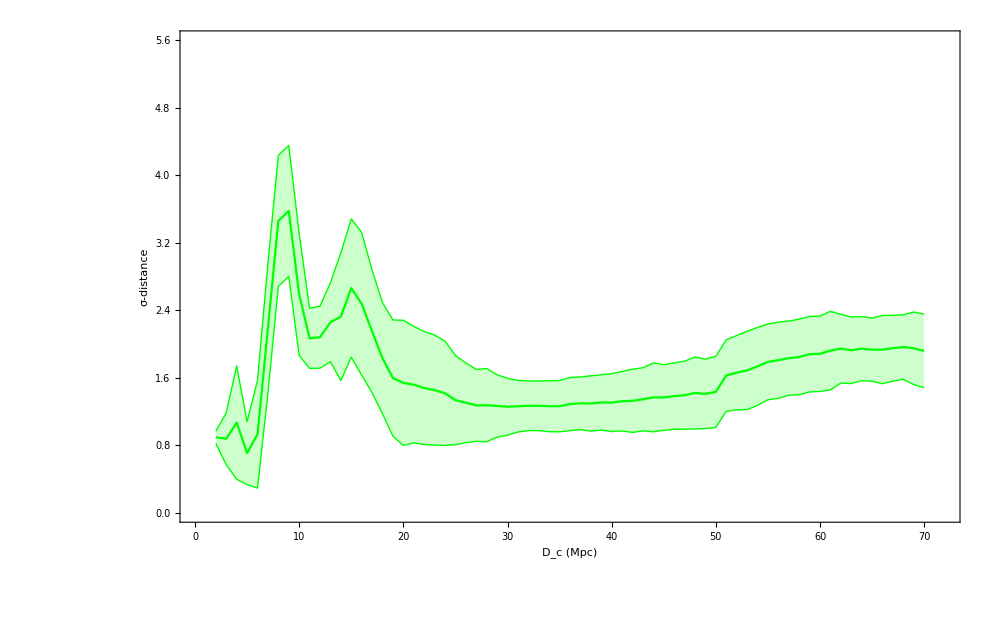

```mathematica
fig2b=ListLinePlot[tabfin,IntervalMarkers->"Bands",Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{Green}},ImageSize->1000, FrameStyle -> Directive[Black, Thick]]
```

```mathematica
Export[NotebookDirectory[]<>"fig2b.pdf",fig2b,ImageResolution->1000];
```

{{2,0.943905},{3,1.60629},{4,2.12167},{5,0.260657},{6,0.185171},{7,1.17647},{8,2.14762},{9,1.63949},{10,1.96879},{11,2.17082},{12,1.93557},{13,2.94547},{14,2.74418},{15,4.35446},{16,2.97051},{17,2.47348},{18,2.13268},{19,2.1522},{20,2.71021},{21,2.98524},{22,2.47383},{23,2.47383},{24,2.52923},{25,2.67035},{26,2.67035},{27,2.67035},{28,2.67035},{29,2.67035},{30,2.67035},{31,2.67035},{32,1.44699},{33,1.48197},{34,1.48197},{35,1.17884},{36,1.17884},{37,1.17884},{38,1.00101},{39,1.00101},{40,1.00101},{41,1.00101},{42,1.00101},{43,1.00101},{44,1.00101},{45,1.24051},{46,1.24051},{47,1.24051},{48,1.4407},{49,1.4407},{50,1.6087},{51,1.94715},{52,1.94715},{53,1.94715},{54,1.94715},{55,1.94715},{56,1.94715},{57,1.94715},{58,2.09794},{59,2.09794},{60,2.09794},{61,1.70399},{62,1.70399},{63,1.70399},{64,1.70399},{65,1.70399},{66,1.70399},{67,2.36877},{68,2.1021},{69,2.1021},{70,2.1021}}

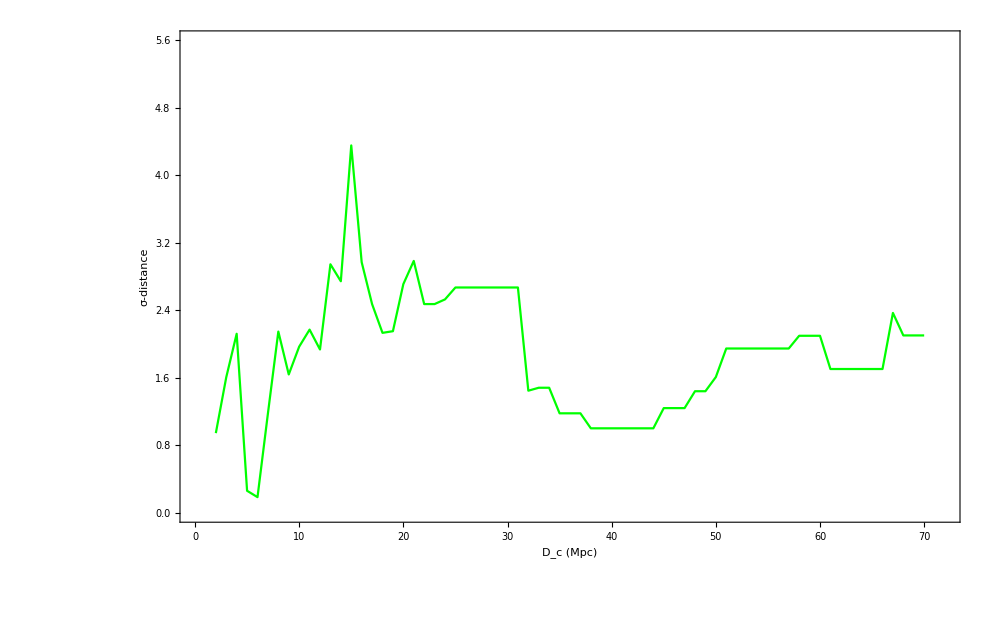

```mathematica
tabfig2a=tabdssd1[[50]]
fig2a=ListLinePlot[tabfig2a,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{Green}},ImageSize->1000, FrameStyle -> Directive[Black, Thick]]
```

```mathematica
Export[NotebookDirectory[]<>"fig2a.pdf",fig2a,ImageResolution->1000];
```

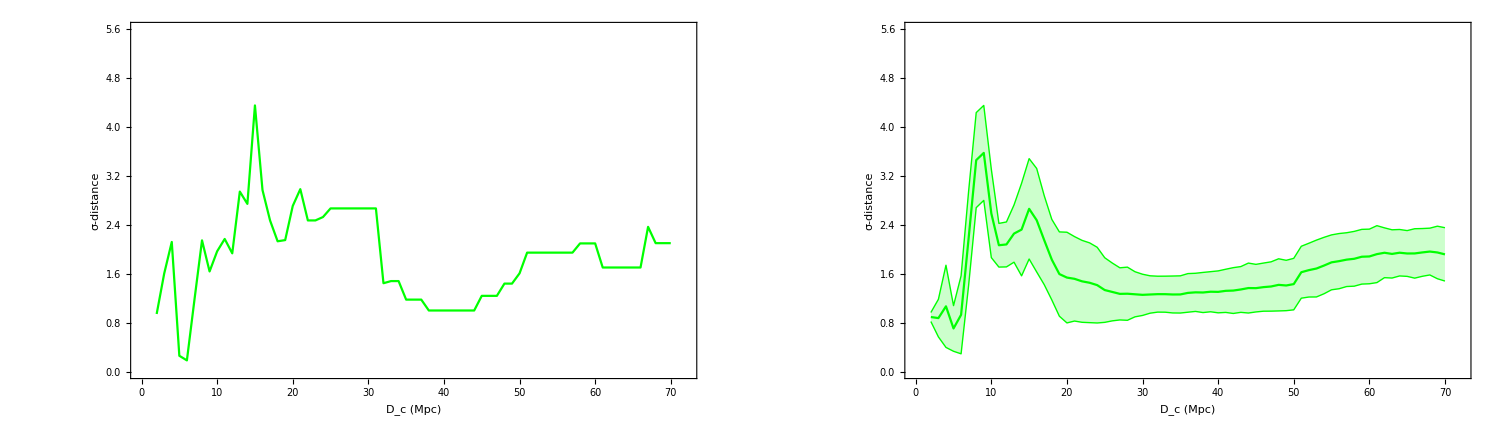

```mathematica
fig2=GraphicsGrid[{{fig2a,fig2b}},ImageSize->1500]
```

```mathematica
Export[NotebookDirectory[]<>"fig2.pdf",fig2,ImageResolution->1000];
```